```mathematica
raspberryPi=FileNameJoin[{"Z:","RbData","2017-12-20"}];
dropBoxOn=FileNameJoin[{"Dropbox","00School","research","DataRuns"}];
If[SystemInformation["Kernel","OperatingSystem"]=="Unix",
folder=FileNameJoin[{"/","home","karl",dropBoxOn}]; ,(* Home coputer is Linux, so needs "/" at beginning *)
folder=FileNameJoin[{"C:","Users","kahrendsen2",dropBoxOn}];(* Lab computer is Windows, so needs "C:" at beginning"*)
];
SetDirectory[folder];
FileNames[]
```

{15-06-09_USBCounterError,15-07-06mockPolarizationData,16-01-14,16-01-21_Data,16-05-25_PolarizationData,16-07-06_PolarizationData,16-08-04_PolarizationData,16-08-07_HeliumTargetPictures,16-08-09_PolarizationData,16-10-17_polarimeter,16-10-27_DataReport,16-11-03_faradayRotation,16-11-07_faradayRotation,16-11-18_faradayRotation,16-12-09_faradayRotation,17-01-31,17-02-17_plusMinus,17-03-06_PlusMinusWavemeter,17-03-10_non-RbFaradayRotation,17-03-15_AimingFor5e12,17-03-15_wavemeterNoRb,17-03-28,17-03-29_pumpLaserFindingCircular,17-03-30_WavemeterReliability,17-04-04_polarization,17-04-06_polarization,17-04-07_wmReliability,17-04-18,17-04-18_polarization,17-04-22,17-04-25_ProbePolarizationDriftOpenChamber,17-04-30_laserReport,17-05-17_DirtyGunRun,17-05-18_ProbeDrift,17-05-19_BetterLaser,17-05-24_SimplifiedPolarization,17-05-25_LaserProfiling,17-05-25_LaserProfiling - Shortcut.lnk,17-06-02,17-06-06_IntensityOfProbeStudy,17-06-11,17-06-13,17-06-16,17-06-17,17-06-25,17-07-01_nRbVsBufferGasAnalysis,17-07-01_PumpLaserAnalysis,17-07-03_lowerNRb_BGPStudy,17-07-03_ProbeDrift,17-07-03_pumpBroadening,17-07-06_lotsOfProbeMeasurements,17-07-06_MagneticField,17-07-06_probePower,17-07-12_polVsPumpPower,17-08-01_rgaInitialScans,17-08-03_redoingSystemDiagnostic,17-08-06_probeDrift,17-08-18_furtherPolarizationStudy,17-08-19_furtherPolarizationStudy2,17-08-22_furtherPolarizationStudyFoundLeak,17-08-29_BvsProbePower_probeDetuneVsMagnetRot,17-09-05_Polarizations_100mTBGP,17-09-20,17-10-03_ElectronGun,17-10-16_ElectronGun,17-10-24_UnpolarizedPolarization,17-10-26_24And30eVRuns,17-10-28_24and30eVRedux,17-11-04_MoreUnpolarizedRuns,17-11-06_UnpolarizedRuns2,17-11-15_BalancedPhotoDetector,17-11-18_SystemDiagnosis,17-12-18_SystemDiagnosis,17-12-20_PolarizingElectrons,18-01-03_PolarizingElectrons,18-01-04_PolarizingElectrons,18-01-10_ChamberWarming,18-01-11_SystemDiagnostics,18-01-12_recreatingPolFigure,18-01-13_recreatingPolFigureIncreasedT,18-01-16_morePolarization,18-01-20_electronPolarization,18-01-25_excitationFunctions,18-01-28_bufferGasPressureVsCounts,18-01-28_exFnCurrentNormalized.png,18-01-28_exFnMolyCounts.png,18-01-28_exFnRawCounts.png,18-01-28_exFnSignalCounts.png,18-01-28_hayesReproduction,18-02-12_polarizedElectrons,18-02-13,18-02-24_DataFrom18-02-13AllElectronEi100,18-02-27,18-03-01,18-03-02,18-03-03,18-03-06_RubidiumOnWalls,18-03-18_100mTorrBGP,18-03-22_Ei=37eV,18-03-23_pumpScan,18-03-24_higherTemps350mTorr,18-03-25_springBreakDataReview,18-03-27_770mTorr,18-03-28_PumpPowerScan,18-04-09_PumpLaserRazorProfile,dataDump,POL2018-03-18.dat,pumpQWP,reallyNiceData,temp,test.png,wavemeterOffsets}

```mathematica
SetDirectory[FileNameJoin[{folder,"18-03-22_Ei=37eV","analysis"}]];
polFileNames=FileNames[StringExpression["POL",__,"_",__,DigitCharacter,".dat"]];
excitationFileNames=FileNames[StringExpression["EX",__,"_",__,DigitCharacter,".dat"]];
scanFiles=FileNames["FDayScan"~~RegularExpression[".{25,25}"]~~"Analysis.dat"];
summaryFiles=FileNames[StringExpression[__,".wdx"]]
```

{190830_BGP=100mTorr-E_i=100-E_h=45.wdx,3-21-18_Ei=37_BGP=100_TempStudy.wdx,3-23-18_Ei=37_BGP=350_pumpDetStep.wdx,3-23-18_Ei=37_BGP=350_TempStudy.wdx,3-25-18_Ei=37_BGP=350_incTemp.wdx,3-25-18_Ei=37_BGP=350_StepTemp.wdx,3-26-18_Ei=35_BGP=770.wdx,3-26-18_Ei=50_BGP=700.wdx,3-27-18_Ei=35_BGP=700_tempStep.wdx}

## Load in all the data files

```mathematica
BGP100={Import["3-21-18_Ei=37_BGP=100_TempStudy.wdx"]};
BGP300={Import["3-23-18_Ei=37_BGP=350_TempStudy.wdx"],Import["3-25-18_Ei=37_BGP=350_StepTemp.wdx"]};
BGP700={Import["3-26-18_Ei=35_BGP=770.wdx"],Import["3-27-18_Ei=35_BGP=700_tempStep.wdx"]};
```

## Combine them into one dataset

```mathematica
dataset=BGP100[[1]];

data=BGP100;
For[i=2,i≤Length[data],i++,
AppendTo[dataset,data[[i]]];
];
data=BGP300;
For[i=1,i≤Length[data],i++,
AppendTo[dataset,data[[i]]];
];

data=BGP700;
For[i=1,i≤Length[data],i++,
AppendTo[dataset,data[[i]]];
];
```

## List the Keys so the variables that can be compared are known

```mathematica
Keys[dataset[[1]]]
```

Dataset[<>]

## Browse the data with a subset of the variables

```mathematica
datasetChoose=Dataset[dataset[All,{"P_e","p0","p1","p3_mag","p3_s2","p_rb","p1err","n_rb","CurrTemp(Res)","CVGauge(N2)(Torr)","pumpLight","time","Comments","CurrenthighEnergySignal","MagnitudeOfCurrent(*10^-X)"}]][Select[#pumpLight!="none"&&#p1>.02&&#p1<.07&]]
```

Dataset[<>]

## Plot Data

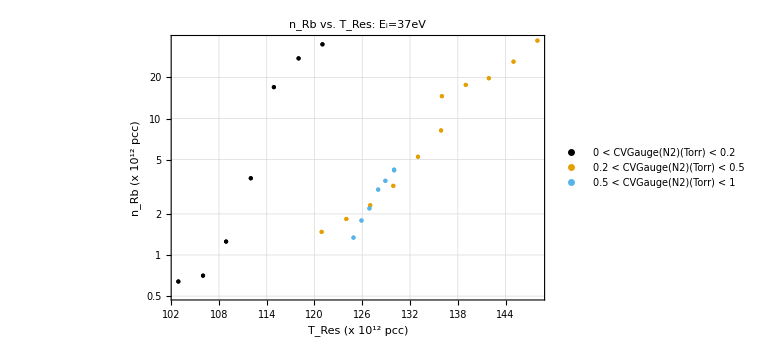

```mathematica
xVar="CurrTemp(Res)";
xLabel="T_Res";
xUnits=" (x 10^12 pcc)";

yVar="n_rb";
yLabel="n_Rb";
yUnits=" (x 10^12 pcc)";

prbVsPePlotRange={{0,1},{0,.15}};
auto={Automatic,Automatic};
plotRange=auto;

vars={xVar,yVar};
frameLabels={xLabel<>xUnits,yLabel<>yUnits};
subtitle="E_i=37eV";
sPlusOnly=dataset[Select[#pumpLight!="none"&(*&#p1>.02&&#p1<.07&&#p0<12&*)]];
plotColorDivisionsVariable="CVGauge(N2)(Torr)";

plotColorDivisions={0,.2,.5,1};
plotArgumentList={};
For[i=1,i<Length[plotColorDivisions],i++,
dataSubset=sPlusOnly[Select[#[plotColorDivisionsVariable]>plotColorDivisions[[i]]&&#[plotColorDivisionsVariable]<plotColorDivisions[[i+1]]&]][Values,vars];
AppendTo[plotArgumentList,Legended[dataSubset,ToString[plotColorDivisions[[i]] ]<>" < "<>plotColorDivisionsVariable<>" < "<>ToString[plotColorDivisions[[i+1]]]]];
];
ListLogPlot[plotArgumentList,PlotRange->plotRange,FrameLabel->frameLabels,PlotLabel->yLabel<> " vs. "<>xLabel<>": "<>subtitle]
```

## Plot Data With Error

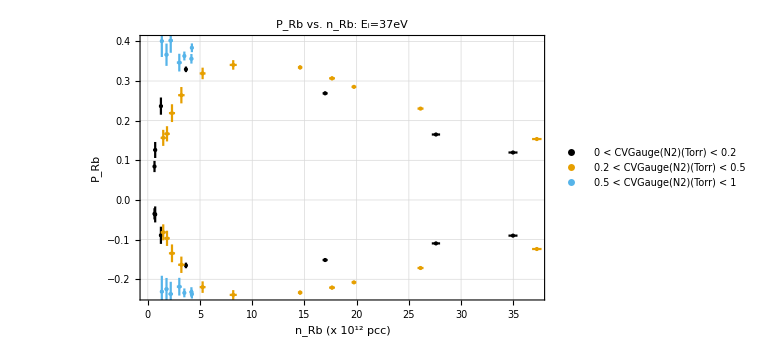

```mathematica
xVar="n_rb";
xLabel="n_Rb";
xUnits=" (x 10^12 pcc)";

yVar="p_rb";
yLabel="P_Rb";
yUnits=" ";

prbVsPePlotRange={{0,1},{0,.15}};
auto={Automatic,Automatic};
plotRange=auto;

vars={xVar,yVar};
frameLabels={xLabel<>xUnits,yLabel<>yUnits};
subtitle="E_i=37eV";

plotColorDivisionsVariable="CVGauge(N2)(Torr)";
plotColorDivisions={0,.2,.5,1};
plotArgumentList={};
For[i=1,i<Length[plotColorDivisions],i++,
dataSubset=GetPlotDataFromDatasetWithError[dataset[Select[#pumpLight!= "none"&]][Select[#[plotColorDivisionsVariable]>plotColorDivisions[[i]]&&#[plotColorDivisionsVariable]<plotColorDivisions[[i+1]]&]],xVar,yVar];
AppendTo[plotArgumentList,Legended[dataSubset,ToString[plotColorDivisions[[i]] ]<>" < "<>plotColorDivisionsVariable<>" < "<>ToString[plotColorDivisions[[i+1]]]]
];

];
ErrorListPlot[plotArgumentList,PlotRange->plotRange,FrameTicks-> Automatic,FrameLabel->frameLabels,PlotLabel->yLabel<> " vs. "<>xLabel<>": "<>subtitle]
```

## Plot Data Over Time

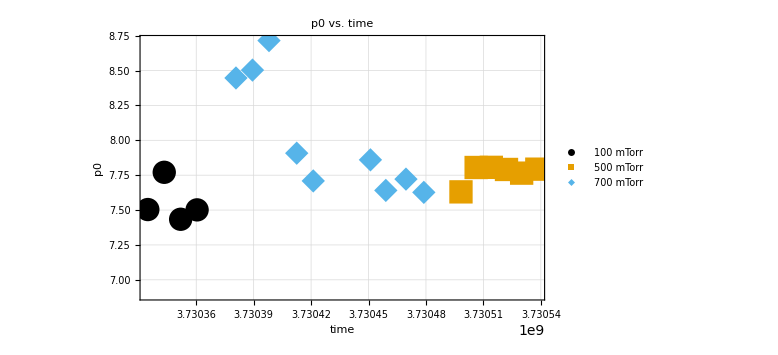

{time,p1}

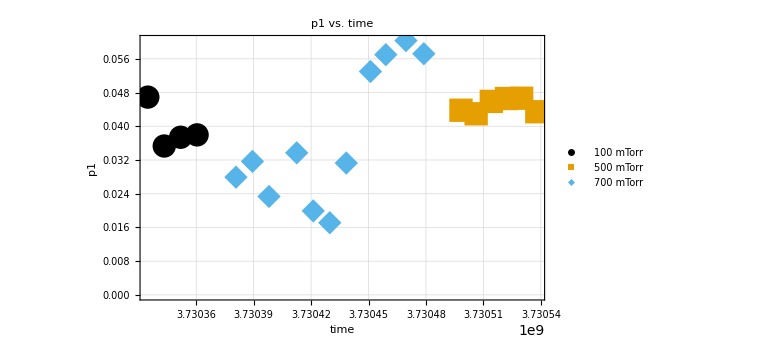

{time,p3_s2}

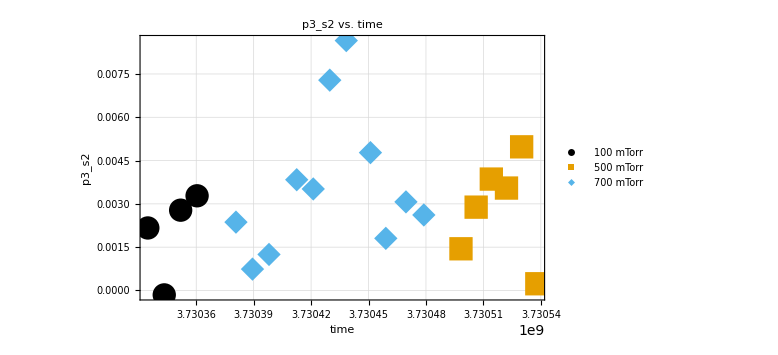

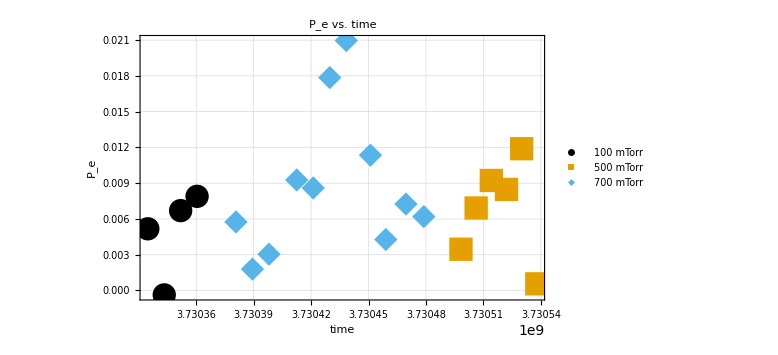

```mathematica
dataset=datasetChoose[Select[#pumpLight=="none"&&#["n_rb"]> 0&&#p0>0&]];

variables={"time","p0"};
plot3=DateListPlot[{Normal[dataset[Select[#["CVGauge(N2)(Torr)"]<.200&]][Values,variables]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .200&&#["CVGauge(N2)(Torr)"]<.600&]][Values,variables]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .600&]][Values,variables]]},Joined->False,ImageSize->Large,PlotLegends->legendLabels,FrameLabel->variables,PlotMarkers->{Automatic,24},LabelStyle->18, PlotLabel->plotLabel]
variables={"time","p1"}
plotLabel:=variables[[2]] <> " vs. "  <> variables[[1]];
legendLabels={"100 mTorr","500 mTorr","700 mTorr"};
plot1=DateListPlot[{Normal[dataset[Select[#["CVGauge(N2)(Torr)"]<.200&]][Values,variables]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .200&&#["CVGauge(N2)(Torr)"]<.600&]][Values,variables]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .600&]][Values,variables]]},Joined->False,ImageSize->Large,PlotLegends->legendLabels,FrameLabel->variables,PlotMarkers->{Automatic,24},LabelStyle->18, PlotLabel->plotLabel]
variables={"time","p3_s2"}
plotLabel:=variables[[2]] <> " vs. "  <> variables[[1]];
legendLabels={"100 mTorr","500 mTorr","700 mTorr"};
plot1=DateListPlot[{Normal[dataset[Select[#["CVGauge(N2)(Torr)"]<.200&]][Values,variables][Values]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .200&&#["CVGauge(N2)(Torr)"]<.600&]][Values,variables][Values]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .600&]][Values,variables][Values]]},Joined->False,ImageSize->Large,PlotLegends->legendLabels,FrameLabel->variables,PlotMarkers->{Automatic,24},LabelStyle->18, PlotLabel->plotLabel]
variables={"time","P_e"};
plot2pt5=DateListPlot[{Normal[dataset[Select[#["CVGauge(N2)(Torr)"]<.200&]][Values,variables]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .200&&#["CVGauge(N2)(Torr)"]<.600&]][Values,variables]],Normal[dataset[Select[#["CVGauge(N2)(Torr)"]≥ .600&]][Values,variables]]},Joined->False,ImageSize->Large,PlotLegends->legendLabels,FrameLabel->variables,PlotMarkers->{Automatic,24},LabelStyle->18, PlotLabel->plotLabel]
```

## Plot Data Over Time With Error

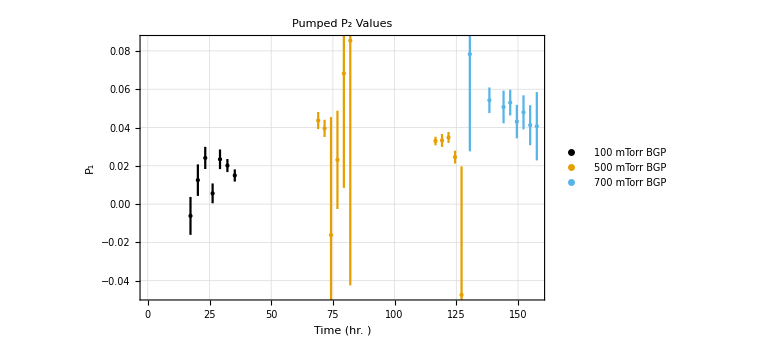

```mathematica
datasetPumpedOnly=dataset[Select[#pumpLight=="s+"&]];
firstDataRunDay=DateObject["March 21, 2018"];
xVar="time";
yVar="P_e";
BGP100error=GetPlotDataFromDatasetWithError[datasetPumpedOnly[Select[#["CVGauge(N2)(Torr)"]<.200&]],xVar,yVar];
BGP500error=GetPlotDataFromDatasetWithError[datasetPumpedOnly[Select[#["CVGauge(N2)(Torr)"]≥ .200&&#["CVGauge(N2)(Torr)"]<.600& ]],xVar,yVar];
BGP700error=GetPlotDataFromDatasetWithError[datasetPumpedOnly[Select[#["CVGauge(N2)(Torr)"]≥ .600&]],xVar,yVar];
ErrorListPlot[{Legended[BGP100error,"100 mTorr BGP"],Legended[BGP500error,"500 mTorr BGP"],Legended[BGP700error,"700 mTorr BGP"]},PlotStyle->colorBlindPallete,FrameLabel->{"Time (hr. )","P_1"},PlotLabel->"Pumped P_2 Values"]
```

## Initialization

```mathematica
black=RGBColor[0/255,0/255,0/255];
orange=RGBColor[230/255,159/255,0];
skyBlue=RGBColor[86/255,180/255,233/255];
bluishGreen=RGBColor[0/255,158/255,115/255];
yellow=RGBColor[240/255,228/255,66/255];
blue=RGBColor[0/255,114/255,178/255];
vermillion=RGBColor[213/255,94/255,0/255];
reddishPurple=RGBColor[204/255,121/255,167/255];
Needs["ErrorBarPlots`"];

colorBlindPallete={orange,skyBlue,bluishGreen,yellow,blue,vermillion,reddishPurple,black}; (*The standard order*)
colorBlindPallete={black,orange,skyBlue,yellow,reddishPurple,vermillion,blue,bluishGreen}; (*Works well with laser goggles*)

SetOptions[Plot,BaseStyle->{FontSize->24},Frame->True,PlotStyle->colorBlindPallete,ImageSize->Large];
SetOptions[ListPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->colorBlindPallete];
SetOptions[ListLogPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->colorBlindPallete];SetOptions[ListLogLinearPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->colorBlindPallete];
SetOptions[ListLogLogPlot,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic,Frame->True,PlotStyle->colorBlindPallete];
SetOptions[DateListPlot,BaseStyle->{FontSize->18,PointSize[Large]},PlotStyle->colorBlindPallete,ImageSize->Large,GridLines->Automatic,Frame->True,LabelStyle->18,PlotMarkers->{Automatic,32}];
SetOptions[BarChart,BaseStyle->{FontSize->18,PointSize[Large]},ImageSize->Large,GridLines->Automatic];

stokesNames={"p0","p1","p2","p3_mag","p3_c2","p3_s2"};
stokesErrNames={"p0err","p1err","p2err","p3_magerr","p3_c2err","p3_s2err"};
```

```mathematica
ListPlotFromDatasetWithError[dataset_,var1_,var2_,plotOptions_:{}]:=Module[{val1,val1err,val2,val2err,ordPair,errData},
errData=GetPlotDataFromDatasetWithError[dataset,var1,var2];
ErrorListPlot[errData,plotOptions]
]

GetPlotDataFromDatasetWithError[dataset_,var1_,var2_]:=Module[{val1,val1err,val2,val2err,ordPair,errData,baseTime,i},
val2=Normal[dataset[Values,var2]];
If[KeyExistsQ[Normal[dataset][[1]],var2<>"err"],
val2err=Normal[dataset[Values,var2<>"err"]],
val2err=ConstantArray[0,Length[val2]]];
val1=Normal[dataset[Values,var1]];
If[KeyExistsQ[Normal[dataset][[1]],var1<>"err"],
val1err=Normal[dataset[Values,var1<>"err"]],
val1err=ConstantArray[0,Length[val1]]];

(* Date objects don't play well with an error plot, so convert date objects to unix time (in seconds), then convert the time to hours. *)
If[var1=="time",
baseTime=val1[[1]];
For[i=1,i≤Length[val1],i++,
val1[[i]]=(UnixTime[val1[[i]]]-UnixTime[firstDataRunDay])/3600;
];];

ordPair=Transpose[{val1,val2}];
errData={};
For [i=1,i≤Length[ordPair],i++,
AppendTo[errData,{ordPair[[i]],ErrorBar[val1err[[i]],val2err[[i]]]}];
];
errData
]
```